```mathematica
ClearAll["Global`*"]
```

Define colors for graphs

```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
```

## System Description

The analysed system is a two-transistor configuration modelled after the electronic Silicon Controlled Resistor (SCR) configuration.
The whole configuration generates a four terminal device, with each terminal being a thermal bath at a particular temperature.

The two quantum thermal transistors S1 and S2 are connected to the four thermal baths B_HOT, B_UC, B_LC and B_COL as follows,
S1 - B_HOT (collector), B_UC (base) and B_LC (emitter)
S2 - B_UC (collector), B_LC (base) and B_COL (emitter).

The thermal bath B_HOT is fixed at a high temperature, while B_COL is fixed at a low temperature. 
The temperatures T_UC and T_LC of the respective upper and lower control terminals (B_UC and B_LC) are not fixed and can vary depending on the internal dynamics.
Once given initial temperature values, these are allowed to naturally relax back to a steady-state temperature.

The two control thermal baths are modelled according to the intermediate bath formalism.
That is, the temperature of these baths increases (decreases) with time if the net inflow of thermal energy to each bath is positive (negative).
In this context, the thermal equilibrium condition would be that the thermal energy inflow from S1 should match the thermal energy outflow to S2.

Each transistor is modelled individually using the techniques developed for Optically Controlled Quantum Thermal Gate paper.

## Deriving the quantum master equation for a single transistor

The index S represents which transistor is considered.

Eigenstates,
|1> =|+z,+z,+z>
|2> =|+z,+z,-z>
|3> =|+z,-z,+z>
|4> =|+z,-z,-z>
|5> =|-z,+z,+z>
|6> =|-z,+z,-z>
|7> =|-z,-z,+z>
|8> =|-z,-z,-z>

### Density matrix

```mathematica
Subscript[ρMatrix, S_][t_]:=Table[Subscript[ρ, S,i,j][t],{i,1,8},{j,1,8}];
MatrixForm[Subscript[ρMatrix, 1][t]]
```

(ρ_(1,1,1)[t] | ρ_(1,1,2)[t] | ρ_(1,1,3)[t] | ρ_(1,1,4)[t] | ρ_(1,1,5)[t] | ρ_(1,1,6)[t] | ρ_(1,1,7)[t] | ρ_(1,1,8)[t]
ρ_(1,2,1)[t] | ρ_(1,2,2)[t] | ρ_(1,2,3)[t] | ρ_(1,2,4)[t] | ρ_(1,2,5)[t] | ρ_(1,2,6)[t] | ρ_(1,2,7)[t] | ρ_(1,2,8)[t]
ρ_(1,3,1)[t] | ρ_(1,3,2)[t] | ρ_(1,3,3)[t] | ρ_(1,3,4)[t] | ρ_(1,3,5)[t] | ρ_(1,3,6)[t] | ρ_(1,3,7)[t] | ρ_(1,3,8)[t]
ρ_(1,4,1)[t] | ρ_(1,4,2)[t] | ρ_(1,4,3)[t] | ρ_(1,4,4)[t] | ρ_(1,4,5)[t] | ρ_(1,4,6)[t] | ρ_(1,4,7)[t] | ρ_(1,4,8)[t]
ρ_(1,5,1)[t] | ρ_(1,5,2)[t] | ρ_(1,5,3)[t] | ρ_(1,5,4)[t] | ρ_(1,5,5)[t] | ρ_(1,5,6)[t] | ρ_(1,5,7)[t] | ρ_(1,5,8)[t]
ρ_(1,6,1)[t] | ρ_(1,6,2)[t] | ρ_(1,6,3)[t] | ρ_(1,6,4)[t] | ρ_(1,6,5)[t] | ρ_(1,6,6)[t] | ρ_(1,6,7)[t] | ρ_(1,6,8)[t]
ρ_(1,7,1)[t] | ρ_(1,7,2)[t] | ρ_(1,7,3)[t] | ρ_(1,7,4)[t] | ρ_(1,7,5)[t] | ρ_(1,7,6)[t] | ρ_(1,7,7)[t] | ρ_(1,7,8)[t]
ρ_(1,8,1)[t] | ρ_(1,8,2)[t] | ρ_(1,8,3)[t] | ρ_(1,8,4)[t] | ρ_(1,8,5)[t] | ρ_(1,8,6)[t] | ρ_(1,8,7)[t] | ρ_(1,8,8)[t])

### System Hamiltonian

```mathematica
Subscript[HsMatrix, S_]:=({{1/2 ℏ (Subscript[ωL, S]+Subscript[ωLM, S]+Subscript[ωM, S]+Subscript[ωMR, S]+Subscript[ωR, S]+Subscript[ωRL, S]), 0, 0, 0, 0, 0, 0, 0}, {0, 1/2 ℏ (Subscript[ωL, S]+Subscript[ωLM, S]+Subscript[ωM, S]-Subscript[ωMR, S]-Subscript[ωR, S]-Subscript[ωRL, S]), 0, 0, 0, 0, 0, 0}, {0, 0, 1/2 ℏ (Subscript[ωL, S]-Subscript[ωLM, S]-Subscript[ωM, S]-Subscript[ωMR, S]+Subscript[ωR, S]+Subscript[ωRL, S]), 0, 0, 0, 0, 0}, {0, 0, 0, 1/2 ℏ (Subscript[ωL, S]-Subscript[ωLM, S]-Subscript[ωM, S]+Subscript[ωMR, S]-Subscript[ωR, S]-Subscript[ωRL, S]), 0, 0, 0, 0}, {0, 0, 0, 0, -1/2 ℏ (Subscript[ωL, S]+Subscript[ωLM, S]-Subscript[ωM, S]-Subscript[ωMR, S]-Subscript[ωR, S]+Subscript[ωRL, S]), 0, 0, 0}, {0, 0, 0, 0, 0, -1/2 ℏ (Subscript[ωL, S]+Subscript[ωLM, S]-Subscript[ωM, S]+Subscript[ωMR, S]+Subscript[ωR, S]-Subscript[ωRL, S]), 0, 0}, {0, 0, 0, 0, 0, 0, -1/2 ℏ (Subscript[ωL, S]-Subscript[ωLM, S]+Subscript[ωM, S]+Subscript[ωMR, S]-Subscript[ωR, S]+Subscript[ωRL, S]), 0}, {0, 0, 0, 0, 0, 0, 0, -1/2 ℏ (Subscript[ωL, S]-Subscript[ωLM, S]+Subscript[ωM, S]-Subscript[ωMR, S]+Subscript[ωR, S]-Subscript[ωRL, S])}})
```

```mathematica
Subscript[HsEVal, S_][i_]:=(Eigenvalues[Subscript[HsMatrix, S]][[{8,1,7,2,4,5,3,6}]])[[i]]
Subscript[HsEVec, S_][i_]:=(Eigenvectors[Subscript[HsMatrix, S]][[{8,1,7,2,4,5,3,6}]])[[i]]
```

Relation between eigenvalues and ωs

```mathematica
ωassum=Flatten[{Table[Subscript[ω, S,i,j]->(Subscript[HsEVal, S][i]-Subscript[HsEVal, S][j] )/ℏ,{S,1,2},{i,1,8},{j,1,8}]}];
```

### Interaction Hamiltonian with the classically modelled optical field

Ω_P represents the strength of the interaction between the device P and the optical field

```mathematica
Subscript[HlMatrix, S_]:= ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -(ℏ Subscript[Ω, S])/2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, -(ℏ Subscript[Ω, S])/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -(ℏ Subscript[Ω, S])/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -(ℏ Subscript[Ω, S])/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

Net optical field induced decaying rate Υ_P[i,j] of the device P from state | i > to state | j > while absorbing energy from the external electric field.
Υs[i,j] is used due to variable naming issues.

```mathematica
Subscript[Υs, S_][i_,j_]:= Subscript[Ω, S]/2 ⅈ(Subscript[ρ, S,i,j][t]-Subscript[ρ, S,j,i][t])
```

### Lindblad terms from environment interactions

Taking results from the previous work

```mathematica
temp1=({{-Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,1}][t]+Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {1,2}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {1,3}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {1,4}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {1,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {1,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {1,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {1,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {2,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,1}][t], -Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,2}][t]+Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {2,3}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {2,4}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {2,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {2,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {2,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {2,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {3,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,1}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {3,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,2}][t], -Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,3}][t]+Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {3,4}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {3,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {3,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {3,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {3,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {4,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,1}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {4,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,2}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {4,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,3}][t], -Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,4}][t]+Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,8}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {4,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {4,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {4,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {4,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {5,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,1}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {5,2}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {5,3}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {5,4}][t], Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,1}][t]-Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {5,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {5,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {5,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {6,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,1}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {6,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,2}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {6,3}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {6,4}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {6,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,5}][t], Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,2}][t]-Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {6,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {6,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {7,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,1}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {7,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,2}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {7,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,3}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {7,4}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {7,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {7,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,6}][t], Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,3}][t]-Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {7,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {8,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,1}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {8,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,2}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {8,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,3}][t], -1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {8,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,4}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {8,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {8,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {8,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,7}][t], Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,4}][t]-Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,8}][t]}});
temp2=({{-Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,1}][t]+Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {1,2}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {1,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {1,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {1,5}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {1,6}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {1,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {1,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {2,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,1}][t], -Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,2}][t]+Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {2,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {2,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {2,5}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {2,6}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {2,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {2,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {3,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,1}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {3,2}][t], Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,1}][t]-Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {3,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {3,5}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {3,6}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {3,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {3,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {4,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,1}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {4,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,2}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {4,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,3}][t], Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,2}][t]-Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {4,5}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {4,6}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {4,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {4,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {5,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,1}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {5,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,2}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {5,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {5,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,4}][t], -Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,5}][t]+Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {5,6}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {5,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {5,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {6,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,1}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {6,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,2}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {6,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {6,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {6,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,5}][t], -Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,6}][t]+Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,8}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {6,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {6,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {7,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,1}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {7,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,2}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {7,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {7,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {7,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,5}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {7,6}][t], Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,5}][t]-Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {7,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {8,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,1}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {8,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,2}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {8,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {8,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {8,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,5}][t], -1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {8,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,6}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {8,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,7}][t], Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,6}][t]-Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,8}][t]}});
temp3=({{-Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,1}][t]+Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {1,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {1,3}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {1,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {1,5}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {1,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {1,7}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {1,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {2,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,1}][t], Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,1}][t]-Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {2,3}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {2,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {2,5}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {2,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {2,7}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {2,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {3,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,1}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {3,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,2}][t], -Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,3}][t]+Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {3,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {3,5}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {3,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {3,7}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {3,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {4,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,1}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {4,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {4,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,3}][t], Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,3}][t]-Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {4,5}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {4,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {4,7}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {4,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {5,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,1}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {5,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {5,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,3}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {5,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,4}][t], -Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,5}][t]+Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {5,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {5,7}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {5,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {6,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,1}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {6,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {6,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,3}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {6,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {6,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,5}][t], Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,5}][t]-Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {6,7}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {6,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {7,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,1}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {7,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {7,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,3}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {7,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {7,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,5}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {7,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,6}][t], -Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,7}][t]+Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,8}][t], -1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {7,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {8,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,1}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {8,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {8,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,3}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {8,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {8,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,5}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {8,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {8,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,7}][t], Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,7}][t]-Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,8}][t]}});
```

```mathematica
temp1/.{Subscript[J, i_]-> Subscript[J, S,i],Subscript[ω, {i_,j_}]-> Subscript[ω, S,i,j],Subscript[ρ, {i_,j_}]->Subscript[ρ, S,i,j],Subscript[NBE, i_]->Subscript[NBE, S,i]}//MatrixForm
temp2/.{Subscript[J, i_]-> Subscript[J, S,i],Subscript[ω, {i_,j_}]-> Subscript[ω, S,i,j],Subscript[ρ, {i_,j_}]->Subscript[ρ, S,i,j],Subscript[NBE, i_]->Subscript[NBE, S,i]}//MatrixForm
temp3/.{Subscript[J, i_]-> Subscript[J, S,i],Subscript[ω, {i_,j_}]-> Subscript[ω, S,i,j],Subscript[ρ, {i_,j_}]->Subscript[ρ, S,i,j],Subscript[NBE, i_]->Subscript[NBE, S,i]}//MatrixForm
```

(-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,1)[t]+J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,5)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,2)[t]-1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,1,2)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,3)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,1,3)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,1,4)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,5)[t]-1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,1,5)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,6)[t]-1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,1,6)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,7)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,1,7)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,1,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,2,1)[t]-1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,1)[t] | -J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,2)[t]+J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,6)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,3)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,2,3)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,2,4)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,2,5)[t]-1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,5)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,6)[t]-1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,2,6)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,7)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,2,7)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,2,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,3,1)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,1)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,3,2)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,2)[t] | -J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,3)[t]+J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,7)[t] | -1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,3,4)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,3,5)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,5)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,3,6)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,6)[t] | -1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,7)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,3,7)[t] | -1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,3,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,4,1)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,1)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,4,2)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,2)[t] | -1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,4,3)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,3)[t] | -J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,4)[t]+J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,8)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,4,5)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,5)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,4,6)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,6)[t] | -1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,4,7)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,7)[t] | -1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,4,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,5,1)[t]-1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,1)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,2)[t]-1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,5,2)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,3)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,5,3)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,5,4)[t] | J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,1)[t]-J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,5)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,6)[t]-1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,5,6)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,7)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,5,7)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,5,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,6,1)[t]-1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,1)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,6,2)[t]-1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,2)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,3)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,6,3)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,6,4)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,6,5)[t]-1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,5)[t] | J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,2)[t]-J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,6)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,7)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,6,7)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,6,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,7,1)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,1)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,7,2)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,2)[t] | -1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,7,3)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,3)[t] | -1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,7,4)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,7,5)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,5)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,7,6)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,6)[t] | J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,3)[t]-J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,7)[t] | -1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,7,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,8,1)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,1)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,8,2)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,2)[t] | -1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,8,3)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,3)[t] | -1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,8,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,4)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,8,5)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,5)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,8,6)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,6)[t] | -1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,8,7)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,7)[t] | J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,4)[t]-J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,8)[t])

(-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,1)[t]+J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,3)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,1,2)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,3)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,1,3)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,1,4)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,5)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,1,5)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,1,6)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,7)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,1,7)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,1,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,2,1)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,1)[t] | -J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,2)[t]+J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,4)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,2,3)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,3)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,2,4)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,5)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,2,5)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,2,6)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,7)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,2,7)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,2,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,1)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,1)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,3,2)[t] | J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,1)[t]-J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,3)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,3,4)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,5)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,3,5)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,3,6)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,7)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,3,7)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,3,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,4,1)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,1)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,2)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,4,3)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,3)[t] | J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,2)[t]-J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,4)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,5)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,4,5)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,4,6)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,7)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,4,7)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,4,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,5,1)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,1)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,5,2)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,2)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,5,3)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,3)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,5,4)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,4)[t] | -J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,5)[t]+J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,7)[t] | -1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,5,6)[t] | -1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,7)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,5,7)[t] | -1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,5,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,6,1)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,1)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,6,2)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,2)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,6,3)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,3)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,6,4)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,4)[t] | -1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,6,5)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,5)[t] | -J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,6)[t]+J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,8)[t] | -1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,6,7)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,7)[t] | -1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,6,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,7,1)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,1)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,7,2)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,2)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,7,3)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,3)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,7,4)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,4)[t] | -1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,7,5)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,5)[t] | -1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,7,6)[t] | J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,5)[t]-J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,7)[t] | -1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,7,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,8,1)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,1)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,8,2)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,2)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,8,3)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,3)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,8,4)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,4)[t] | -1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,8,5)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,5)[t] | -1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,8,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,6)[t] | -1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,8,7)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,7)[t] | J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,6)[t]-J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,8)[t])

(-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,1)[t]+J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,2)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,2)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,1,2)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,1,3)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,1,4)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,5)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,1,5)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,6)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,1,6)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,1,7)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,1,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,1)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,1)[t] | J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,1)[t]-J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,2)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,2,3)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,2,4)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,5)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,2,5)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,6)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,2,6)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,2,7)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,2,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,3,1)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,1)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,3,2)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,2)[t] | -J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,3)[t]+J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,4)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,3,4)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,5)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,3,5)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,6)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,3,6)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,3,7)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,3,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,4,1)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,1)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,4,2)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,2)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,3)[t] | J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,3)[t]-J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,4)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,5)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,4,5)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,6)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,4,6)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,4,7)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,4,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,5,1)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,1)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,5,2)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,2)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,5,3)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,3)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,5,4)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,4)[t] | -J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,5)[t]+J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,6)[t] | -1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,6)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,5,6)[t] | -1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,5,7)[t] | -1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,5,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,6,1)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,1)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,6,2)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,2)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,6,3)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,3)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,6,4)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,4)[t] | -1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,6,5)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,5)[t] | J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,5)[t]-J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,6)[t] | -1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,6,7)[t] | -1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,6,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,7,1)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,1)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,7,2)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,2)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,7,3)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,3)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,7,4)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,4)[t] | -1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,7,5)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,5)[t] | -1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,7,6)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,6)[t] | -J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,7)[t]+J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,8)[t] | -1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,7,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,8,1)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,1)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,8,2)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,2)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,8,3)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,3)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,8,4)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,4)[t] | -1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,8,5)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,5)[t] | -1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,8,6)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,6)[t] | -1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,8,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,7)[t] | J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,7)[t]-J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,8)[t])

Linbladian for the Markovian quantum master equation,

```mathematica
Subscript[LinMatrix, S_,1]:=({{-Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,1][t]+Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,1,2][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,1,3][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,1,4][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,1,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,1,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,1,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,1,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,2,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,1][t], -Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,2][t]+Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,2,3][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,2,4][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,2,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,2,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,2,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,2,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,3,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,1][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,3,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,2][t], -Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,3][t]+Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,3,4][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,3,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,3,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,3,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,3,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,4,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,1][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,4,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,2][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,4,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,3][t], -Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,4][t]+Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,8][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,4,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,4,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,4,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,4,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,5,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,1][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,5,2][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,5,3][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,5,4][t], Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,1][t]-Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,5,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,5,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,5,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,6,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,1][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,6,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,2][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,6,3][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,6,4][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,6,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,5][t], Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,2][t]-Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,6,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,6,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,7,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,1][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,7,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,2][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,7,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,3][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,7,4][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,7,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,7,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,6][t], Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,3][t]-Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,7,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,8,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,1][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,8,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,2][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,8,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,3][t], -1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,8,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,4][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,8,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,8,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,8,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,7][t], Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,4][t]-Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,8][t]}})
Subscript[LinMatrix, S_,2]:=({{-Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,1][t]+Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,1,2][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,1,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,1,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,1,5][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,1,6][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,1,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,1,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,2,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,1][t], -Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,2][t]+Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,2,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,2,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,2,5][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,2,6][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,2,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,2,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,3,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,1][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,3,2][t], Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,1][t]-Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,3,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,3,5][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,3,6][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,3,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,3,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,4,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,1][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,4,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,2][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,4,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,3][t], Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,2][t]-Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,4,5][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,4,6][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,4,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,4,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,5,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,1][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,5,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,2][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,5,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,5,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,4][t], -Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,5][t]+Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,5,6][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,5,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,5,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,6,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,1][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,6,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,2][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,6,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,6,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,6,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,5][t], -Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,6][t]+Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,8][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,6,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,6,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,7,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,1][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,7,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,2][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,7,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,7,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,7,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,5][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,7,6][t], Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,5][t]-Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,7,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,8,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,1][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,8,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,2][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,8,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,8,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,8,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,5][t], -1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,8,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,6][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,8,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,7][t], Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,6][t]-Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,8][t]}})
Subscript[LinMatrix, S_,3]:=({{-Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,1][t]+Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,1,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,1,3][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,1,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,1,5][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,1,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,1,7][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,1,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,2,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,1][t], Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,1][t]-Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,2,3][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,2,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,2,5][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,2,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,2,7][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,2,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,3,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,1][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,3,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,2][t], -Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,3][t]+Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,3,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,3,5][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,3,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,3,7][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,3,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,4,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,1][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,4,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,4,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,3][t], Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,3][t]-Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,4,5][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,4,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,4,7][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,4,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,5,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,1][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,5,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,5,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,3][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,5,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,4][t], -Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,5][t]+Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,5,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,5,7][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,5,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,6,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,1][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,6,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,6,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,3][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,6,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,6,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,5][t], Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,5][t]-Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,6,7][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,6,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,7,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,1][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,7,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,7,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,3][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,7,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,7,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,5][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,7,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,6][t], -Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,7][t]+Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,8][t], -1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,7,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,8,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,1][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,8,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,8,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,3][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,8,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,8,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,5][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,8,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,8,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,7][t], Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,7][t]-Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,8][t]}})
```

Net thermal decaying rate Τ_(S,P)[i,j] of component S from state | i > to state | j > while releasing energy to reservoir P. Note i > j.
Τs_(S,P)[i,j] is used due to variable naming issues.

```mathematica
Subscript[Τs, S_,P_][i_,j_]:=Subscript[J, S,P][Subscript[ω, S,i,j]]((1+Subscript[NBE, S,P][Subscript[ω, S,i,j]])Subscript[ρ, S,i,i][t]-Subscript[NBE, S,P][Subscript[ω, S,i,j]]Subscript[ρ, S,j,j][t])
```

Mathematica function for arithmetically proper replacements,

```mathematica
ReplaceArithmetically[expr_,orig_,repl_]:=
Module[{f},
(*Actual replacement function, but it is not Listable*)
f[exprs_,origs_,repls_]:=Module[{q,r},
{q,r}=PolynomialReduce[exprs,origs,{}];
q.repls+r
];
(*Construct for making the function Listable in only the first argument*)
Function[t,f[t,orig,repl],{Listable}][expr]
]
```

```mathematica
ReplaceArithmetically[Subscript[LinMatrix, 1,1],
Flatten[Table[Subscript[Τs, S,P][i,j],{S,1,2},{P,1,3},{i,1,8},{j,1,8}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{S,1,2},{P,1,3},{i,1,8},{j,1,8}]]
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinMatrix, 1,2],
Flatten[Table[Subscript[Τs, S,P][i,j],{S,1,2},{P,1,3},{i,1,8},{j,1,8}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{S,1,2},{P,1,3},{i,1,8},{j,1,8}]]
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinMatrix, 1,3],
Flatten[Table[Subscript[Τs, S,P][i,j],{S,1,2},{P,1,3},{i,1,8},{j,1,8}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{S,1,2},{P,1,3},{i,1,8},{j,1,8}]]
];
MatrixForm[%]
```

(Τ_(1,1)[5,1] | 1/2 (-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,2)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,1,2)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,3)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,1,3)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,4)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,1,4)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,1,5)[t]-2 J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,5)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,1,6)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,6)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,1,6)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,1,7)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,7)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,1,7)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,1,8)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,8)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,1,8)[t])
1/2 (-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,2,1)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,1)[t]) | Τ_(1,1)[6,2] | 1/2 (-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,3)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,2,3)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,4)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,2,4)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,2,5)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,2,5)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,5)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,2,6)[t]-2 J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,6)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,2,7)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,7)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,2,7)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,2,8)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,8)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,2,8)[t])
1/2 (-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,3,1)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,1)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,3,2)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,2)[t]) | Τ_(1,1)[7,3] | 1/2 (-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,4)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,3,4)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,3,5)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,3,5)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,5)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,3,6)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,3,6)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,6)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,3,7)[t]-2 J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,7)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,3,8)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,8)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,3,8)[t])
1/2 (-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,4,1)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,1)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,4,2)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,2)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,4,3)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,3)[t]) | Τ_(1,1)[8,4] | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,4,5)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,4,5)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,5)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,4,6)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,4,6)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,6)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,4,7)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,4,7)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,7)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,4,8)[t]-2 J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,8)[t])
1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,1)[t]-2 J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,1)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,2)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,2)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,5,2)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,3)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,3)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,5,3)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,4)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,4)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,5,4)[t]) | -Τ_(1,1)[5,1] | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,6)[t]-J_(1,1)[ω_(1,6,2)] ρ_(1,5,6)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,6)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,5,6)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,7)[t]-J_(1,1)[ω_(1,7,3)] ρ_(1,5,7)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,7)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,5,7)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,8)[t]-J_(1,1)[ω_(1,8,4)] ρ_(1,5,8)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,8)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,5,8)[t])
1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,6,1)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,6,1)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,1)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,6,2)[t]-2 J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,2)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,6,3)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,3)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,6,3)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,6,4)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,4)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,6,4)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,6,5)[t]-J_(1,1)[ω_(1,6,2)] ρ_(1,6,5)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,6,5)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,5)[t]) | -Τ_(1,1)[6,2] | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,6,7)[t]-J_(1,1)[ω_(1,7,3)] ρ_(1,6,7)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,7)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,6,7)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,6,8)[t]-J_(1,1)[ω_(1,8,4)] ρ_(1,6,8)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,8)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,6,8)[t])
1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,7,1)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,7,1)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,1)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,7,2)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,7,2)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,2)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,7,3)[t]-2 J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,3)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,7,4)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,4)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,7,4)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,7,5)[t]-J_(1,1)[ω_(1,7,3)] ρ_(1,7,5)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,7,5)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,5)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,7,6)[t]-J_(1,1)[ω_(1,7,3)] ρ_(1,7,6)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,7,6)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,6)[t]) | -Τ_(1,1)[7,3] | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,7,8)[t]-J_(1,1)[ω_(1,8,4)] ρ_(1,7,8)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,8)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,7,8)[t])
1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,8,1)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,8,1)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,1)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,8,2)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,8,2)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,2)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,8,3)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,8,3)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,3)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,8,4)[t]-2 J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,4)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,8,5)[t]-J_(1,1)[ω_(1,8,4)] ρ_(1,8,5)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,8,5)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,5)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,8,6)[t]-J_(1,1)[ω_(1,8,4)] ρ_(1,8,6)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,8,6)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,6)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,8,7)[t]-J_(1,1)[ω_(1,8,4)] ρ_(1,8,7)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,8,7)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,7)[t]) | -Τ_(1,1)[8,4])

(Τ_(1,2)[3,1] | 1/2 (-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,2)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,1,2)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,1,3)[t]-2 J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,3)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,1,4)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,4)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,1,4)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,5)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,1,5)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,6)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,1,6)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,1,7)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,7)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,1,7)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,1,8)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,8)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,1,8)[t])
1/2 (-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,2,1)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,1)[t]) | Τ_(1,2)[4,2] | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,2,3)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,2,3)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,3)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,2,4)[t]-2 J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,4)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,5)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,2,5)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,6)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,2,6)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,2,7)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,7)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,2,7)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,2,8)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,8)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,2,8)[t])
1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,1)[t]-2 J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,1)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,2)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,2)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,3,2)[t]) | -Τ_(1,2)[3,1] | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,4)[t]-J_(1,2)[ω_(1,4,2)] ρ_(1,3,4)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,4)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,3,4)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,5)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,5)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,3,5)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,6)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,6)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,3,6)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,7)[t]-J_(1,2)[ω_(1,7,5)] ρ_(1,3,7)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,7)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,3,7)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,8)[t]-J_(1,2)[ω_(1,8,6)] ρ_(1,3,8)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,8)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,3,8)[t])
1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,4,1)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,4,1)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,1)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,4,2)[t]-2 J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,2)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,4,3)[t]-J_(1,2)[ω_(1,4,2)] ρ_(1,4,3)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,4,3)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,3)[t]) | -Τ_(1,2)[4,2] | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,4,5)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,5)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,4,5)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,4,6)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,6)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,4,6)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,4,7)[t]-J_(1,2)[ω_(1,7,5)] ρ_(1,4,7)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,7)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,4,7)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,4,8)[t]-J_(1,2)[ω_(1,8,6)] ρ_(1,4,8)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,8)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,4,8)[t])
1/2 (-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,5,1)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,1)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,5,2)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,2)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,5,3)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,5,3)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,3)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,5,4)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,5,4)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,4)[t]) | Τ_(1,2)[7,5] | 1/2 (-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,6)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,5,6)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,5,7)[t]-2 J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,7)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,5,8)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,8)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,5,8)[t])
1/2 (-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,6,1)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,1)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,6,2)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,2)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,6,3)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,6,3)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,3)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,6,4)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,6,4)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,4)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,6,5)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,5)[t]) | Τ_(1,2)[8,6] | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,6,7)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,6,7)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,7)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,6,8)[t]-2 J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,8)[t])
1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,7,1)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,7,1)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,1)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,7,2)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,7,2)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,2)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,7,3)[t]-J_(1,2)[ω_(1,7,5)] ρ_(1,7,3)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,7,3)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,3)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,7,4)[t]-J_(1,2)[ω_(1,7,5)] ρ_(1,7,4)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,7,4)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,4)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,7,5)[t]-2 J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,5)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,7,6)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,6)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,7,6)[t]) | -Τ_(1,2)[7,5] | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,7,8)[t]-J_(1,2)[ω_(1,8,6)] ρ_(1,7,8)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,8)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,7,8)[t])
1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,8,1)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,8,1)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,1)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,8,2)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,8,2)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,2)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,8,3)[t]-J_(1,2)[ω_(1,8,6)] ρ_(1,8,3)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,8,3)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,3)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,8,4)[t]-J_(1,2)[ω_(1,8,6)] ρ_(1,8,4)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,8,4)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,4)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,8,5)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,8,5)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,5)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,8,6)[t]-2 J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,6)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,8,7)[t]-J_(1,2)[ω_(1,8,6)] ρ_(1,8,7)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,8,7)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,7)[t]) | -Τ_(1,2)[8,6])

(Τ_(1,3)[2,1] | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,1,2)[t]-2 J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,2)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,3)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,1,3)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,1,4)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,4)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,1,4)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,5)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,1,5)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,1,6)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,6)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,1,6)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,7)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,1,7)[t]) | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,1,8)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,8)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,1,8)[t])
1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,1)[t]-2 J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,1)[t]) | -Τ_(1,3)[2,1] | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,3)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,3)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,2,3)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,4)[t]-J_(1,3)[ω_(1,4,3)] ρ_(1,2,4)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,4)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,2,4)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,5)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,5)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,2,5)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,6)[t]-J_(1,3)[ω_(1,6,5)] ρ_(1,2,6)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,6)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,2,6)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,7)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,7)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,2,7)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,8)[t]-J_(1,3)[ω_(1,8,7)] ρ_(1,2,8)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,8)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,2,8)[t])
1/2 (-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,3,1)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,1)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,3,2)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,3,2)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,2)[t]) | Τ_(1,3)[4,3] | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,3,4)[t]-2 J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,4)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,5)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,3,5)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,3,6)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,6)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,3,6)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,7)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,3,7)[t]) | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,3,8)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,8)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,3,8)[t])
1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,4,1)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,4,1)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,1)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,4,2)[t]-J_(1,3)[ω_(1,4,3)] ρ_(1,4,2)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,4,2)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,2)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,4,3)[t]-2 J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,3)[t]) | -Τ_(1,3)[4,3] | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,4,5)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,5)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,4,5)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,4,6)[t]-J_(1,3)[ω_(1,6,5)] ρ_(1,4,6)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,6)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,4,6)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,4,7)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,7)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,4,7)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,4,8)[t]-J_(1,3)[ω_(1,8,7)] ρ_(1,4,8)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,8)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,4,8)[t])
1/2 (-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,5,1)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,1)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,5,2)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,5,2)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,2)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,5,3)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,3)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,5,4)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,5,4)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,4)[t]) | Τ_(1,3)[6,5] | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,5,6)[t]-2 J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,6)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,7)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,5,7)[t]) | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,5,8)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,8)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,5,8)[t])
1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,6,1)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,6,1)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,1)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,6,2)[t]-J_(1,3)[ω_(1,6,5)] ρ_(1,6,2)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,6,2)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,2)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,6,3)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,6,3)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,3)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,6,4)[t]-J_(1,3)[ω_(1,6,5)] ρ_(1,6,4)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,6,4)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,4)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,6,5)[t]-2 J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,5)[t]) | -Τ_(1,3)[6,5] | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,6,7)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,7)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,6,7)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,6,8)[t]-J_(1,3)[ω_(1,8,7)] ρ_(1,6,8)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,8)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,6,8)[t])
1/2 (-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,7,1)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,1)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,7,2)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,7,2)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,2)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,7,3)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,3)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,7,4)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,7,4)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,4)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,7,5)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,5)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,7,6)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,7,6)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,6)[t]) | Τ_(1,3)[8,7] | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,7,8)[t]-2 J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,8)[t])
1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,8,1)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,8,1)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,1)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,8,2)[t]-J_(1,3)[ω_(1,8,7)] ρ_(1,8,2)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,8,2)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,2)[t]) | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,8,3)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,8,3)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,3)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,8,4)[t]-J_(1,3)[ω_(1,8,7)] ρ_(1,8,4)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,8,4)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,4)[t]) | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,8,5)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,8,5)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,5)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,8,6)[t]-J_(1,3)[ω_(1,8,7)] ρ_(1,8,6)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,8,6)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,6)[t]) | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,8,7)[t]-2 J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,7)[t]) | -Τ_(1,3)[8,7])

### Quantum Markovian master equation

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, S_,P_][ω_]->Subscript[κ, S,P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
Subscript[RHSfield, S_]:=-ⅈ/ℏ(Subscript[HlMatrix, S].Subscript[ρMatrix, S][t]-Subscript[ρMatrix, S][t].Subscript[HlMatrix, S]);

Subscript[RHS, S_]:=Subscript[RHSfield, S]+Subscript[LinMatrix, S,1]+Subscript[LinMatrix, S,2]+Subscript[LinMatrix, S,3];

{MatrixForm[Subscript[RHS, 1]],MatrixForm[Subscript[RHS, 2]]}
```

{(1),(1)}
 |  |  |  |

```mathematica
Subscript[LHS, S_]:=D[Subscript[ρMatrix, S][t], t];

{MatrixForm[Subscript[LHS, 1]],MatrixForm[Subscript[LHS, 2]]}
```

{(ρ_(1,1,1)'[t] | ρ_(1,1,2)'[t] | ρ_(1,1,3)'[t] | ρ_(1,1,4)'[t] | ρ_(1,1,5)'[t] | ρ_(1,1,6)'[t] | ρ_(1,1,7)'[t] | ρ_(1,1,8)'[t]
ρ_(1,2,1)'[t] | ρ_(1,2,2)'[t] | ρ_(1,2,3)'[t] | ρ_(1,2,4)'[t] | ρ_(1,2,5)'[t] | ρ_(1,2,6)'[t] | ρ_(1,2,7)'[t] | ρ_(1,2,8)'[t]
ρ_(1,3,1)'[t] | ρ_(1,3,2)'[t] | ρ_(1,3,3)'[t] | ρ_(1,3,4)'[t] | ρ_(1,3,5)'[t] | ρ_(1,3,6)'[t] | ρ_(1,3,7)'[t] | ρ_(1,3,8)'[t]
ρ_(1,4,1)'[t] | ρ_(1,4,2)'[t] | ρ_(1,4,3)'[t] | ρ_(1,4,4)'[t] | ρ_(1,4,5)'[t] | ρ_(1,4,6)'[t] | ρ_(1,4,7)'[t] | ρ_(1,4,8)'[t]
ρ_(1,5,1)'[t] | ρ_(1,5,2)'[t] | ρ_(1,5,3)'[t] | ρ_(1,5,4)'[t] | ρ_(1,5,5)'[t] | ρ_(1,5,6)'[t] | ρ_(1,5,7)'[t] | ρ_(1,5,8)'[t]
ρ_(1,6,1)'[t] | ρ_(1,6,2)'[t] | ρ_(1,6,3)'[t] | ρ_(1,6,4)'[t] | ρ_(1,6,5)'[t] | ρ_(1,6,6)'[t] | ρ_(1,6,7)'[t] | ρ_(1,6,8)'[t]
ρ_(1,7,1)'[t] | ρ_(1,7,2)'[t] | ρ_(1,7,3)'[t] | ρ_(1,7,4)'[t] | ρ_(1,7,5)'[t] | ρ_(1,7,6)'[t] | ρ_(1,7,7)'[t] | ρ_(1,7,8)'[t]
ρ_(1,8,1)'[t] | ρ_(1,8,2)'[t] | ρ_(1,8,3)'[t] | ρ_(1,8,4)'[t] | ρ_(1,8,5)'[t] | ρ_(1,8,6)'[t] | ρ_(1,8,7)'[t] | ρ_(1,8,8)'[t]),(ρ_(2,1,1)'[t] | ρ_(2,1,2)'[t] | ρ_(2,1,3)'[t] | ρ_(2,1,4)'[t] | ρ_(2,1,5)'[t] | ρ_(2,1,6)'[t] | ρ_(2,1,7)'[t] | ρ_(2,1,8)'[t]
ρ_(2,2,1)'[t] | ρ_(2,2,2)'[t] | ρ_(2,2,3)'[t] | ρ_(2,2,4)'[t] | ρ_(2,2,5)'[t] | ρ_(2,2,6)'[t] | ρ_(2,2,7)'[t] | ρ_(2,2,8)'[t]
ρ_(2,3,1)'[t] | ρ_(2,3,2)'[t] | ρ_(2,3,3)'[t] | ρ_(2,3,4)'[t] | ρ_(2,3,5)'[t] | ρ_(2,3,6)'[t] | ρ_(2,3,7)'[t] | ρ_(2,3,8)'[t]
ρ_(2,4,1)'[t] | ρ_(2,4,2)'[t] | ρ_(2,4,3)'[t] | ρ_(2,4,4)'[t] | ρ_(2,4,5)'[t] | ρ_(2,4,6)'[t] | ρ_(2,4,7)'[t] | ρ_(2,4,8)'[t]
ρ_(2,5,1)'[t] | ρ_(2,5,2)'[t] | ρ_(2,5,3)'[t] | ρ_(2,5,4)'[t] | ρ_(2,5,5)'[t] | ρ_(2,5,6)'[t] | ρ_(2,5,7)'[t] | ρ_(2,5,8)'[t]
ρ_(2,6,1)'[t] | ρ_(2,6,2)'[t] | ρ_(2,6,3)'[t] | ρ_(2,6,4)'[t] | ρ_(2,6,5)'[t] | ρ_(2,6,6)'[t] | ρ_(2,6,7)'[t] | ρ_(2,6,8)'[t]
ρ_(2,7,1)'[t] | ρ_(2,7,2)'[t] | ρ_(2,7,3)'[t] | ρ_(2,7,4)'[t] | ρ_(2,7,5)'[t] | ρ_(2,7,6)'[t] | ρ_(2,7,7)'[t] | ρ_(2,7,8)'[t]
ρ_(2,8,1)'[t] | ρ_(2,8,2)'[t] | ρ_(2,8,3)'[t] | ρ_(2,8,4)'[t] | ρ_(2,8,5)'[t] | ρ_(2,8,6)'[t] | ρ_(2,8,7)'[t] | ρ_(2,8,8)'[t])}

Markovian quantum master equation for a general density matrix,

```mathematica
Subscript[motioneq, S_]:=Flatten[Solve[Subscript[LHS, S]==Subscript[RHS, S],Flatten[Table[Subscript[ρ, S,i,j]'[t],{i,1,8},{j,1,8}]]]/.Rule->Equal]
```

Separate diagonal and off diagonal equations,

```mathematica
Subscript[motioneqdiag, S_]:=Subscript[motioneq, S][[1;; ;;9]];
Subscript[motioneqoffdiag, S_]:=Delete[Subscript[motioneq, S],Table[{1+9i},{i,0,7}]];
```

Diagonals of the Markovian quantum master equation simplified to transition rates,

```mathematica
Subscript[motioneqdiagtran, S_]:=
ApplySides[
ReplaceArithmetically[Simplify[#],
Flatten[{Table[Subscript[Τs, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}]
]&,Subscript[motioneqdiag, S]]
```

### Equations of motion for the individual transistors

Actual equations for population densities (i.e. diagonal elements of the density matrix),

```mathematica
{Subscript[motioneqdiag, 1],Subscript[motioneqdiag, 2]};
```

Simplified version of the same equations,

```mathematica
Subscript[motioneqdiagtran, 1]
Subscript[motioneqdiagtran, 2]
```

{ρ_(1,1,1)'[t]==Τ_(1,1)[5,1]+Τ_(1,2)[3,1]+Τ_(1,3)[2,1],ρ_(1,2,2)'[t]==-Υ_1[2,4]+Τ_(1,1)[6,2]+Τ_(1,2)[4,2]-Τ_(1,3)[2,1],ρ_(1,3,3)'[t]==Τ_(1,1)[7,3]-Τ_(1,2)[3,1]+Τ_(1,3)[4,3],ρ_(1,4,4)'[t]==Υ_1[2,4]+Τ_(1,1)[8,4]-Τ_(1,2)[4,2]-Τ_(1,3)[4,3],ρ_(1,5,5)'[t]==-Υ_1[5,7]-Τ_(1,1)[5,1]+Τ_(1,2)[7,5]+Τ_(1,3)[6,5],ρ_(1,6,6)'[t]==-Τ_(1,1)[6,2]+Τ_(1,2)[8,6]-Τ_(1,3)[6,5],ρ_(1,7,7)'[t]==Υ_1[5,7]-Τ_(1,1)[7,3]-Τ_(1,2)[7,5]+Τ_(1,3)[8,7],ρ_(1,8,8)'[t]==-Τ_(1,1)[8,4]-Τ_(1,2)[8,6]-Τ_(1,3)[8,7]}

{ρ_(2,1,1)'[t]==Τ_(2,1)[5,1]+Τ_(2,2)[3,1]+Τ_(2,3)[2,1],ρ_(2,2,2)'[t]==-Υ_2[2,4]+Τ_(2,1)[6,2]+Τ_(2,2)[4,2]-Τ_(2,3)[2,1],ρ_(2,3,3)'[t]==Τ_(2,1)[7,3]-Τ_(2,2)[3,1]+Τ_(2,3)[4,3],ρ_(2,4,4)'[t]==Υ_2[2,4]+Τ_(2,1)[8,4]-Τ_(2,2)[4,2]-Τ_(2,3)[4,3],ρ_(2,5,5)'[t]==-Υ_2[5,7]-Τ_(2,1)[5,1]+Τ_(2,2)[7,5]+Τ_(2,3)[6,5],ρ_(2,6,6)'[t]==-Τ_(2,1)[6,2]+Τ_(2,2)[8,6]-Τ_(2,3)[6,5],ρ_(2,7,7)'[t]==Υ_2[5,7]-Τ_(2,1)[7,3]-Τ_(2,2)[7,5]+Τ_(2,3)[8,7],ρ_(2,8,8)'[t]==-Τ_(2,1)[8,4]-Τ_(2,2)[8,6]-Τ_(2,3)[8,7]}

### Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, S_,P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, S,P]))-1);
```

Calculate heat current inflow, from the thermal bath into the transistor

```mathematica
Subscript[HsMatrixSimp, S_]:=DiagonalMatrix[ℏ{Subscript[ω, S,1],Subscript[ω, S,2],Subscript[ω, S,3],Subscript[ω, S,4],Subscript[ω, S,5],Subscript[ω, S,6],Subscript[ω, S,7],Subscript[ω, S,8]}];
ωassum1={Table[Subscript[ω, S,i]-> Subscript[HsMatrix, S][[i,i]]/ℏ,{S,1,2},{i,1,8}]};
```

```mathematica
Subscript[EngyFlowIn, S_,P_]:=Tr[Subscript[LinMatrix, S,P].Subscript[HsMatrixSimp, S]]
Subscript[EngyFlowInField, S_]:=Tr[Subscript[RHSfield, S].Subscript[HsMatrixSimp, S]]
```

```mathematica
ReplaceArithmetically[Subscript[EngyFlowIn, 1,1],
Flatten[{Table[Subscript[Τs, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}]
]

ReplaceArithmetically[Subscript[EngyFlowIn, 1,2],
Flatten[{Table[Subscript[Τs, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}]
]

ReplaceArithmetically[Subscript[EngyFlowIn, 1,3],
Flatten[{Table[Subscript[Τs, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}]
]

ReplaceArithmetically[Subscript[EngyFlowInField, 1],
Flatten[{Table[Subscript[Τs, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}]
];
Simplify[%]
```

(ℏ ω_(1,1)-ℏ ω_(1,5)) Τ_(1,1)[5,1]+(ℏ ω_(1,2)-ℏ ω_(1,6)) Τ_(1,1)[6,2]+(ℏ ω_(1,3)-ℏ ω_(1,7)) Τ_(1,1)[7,3]+(ℏ ω_(1,4)-ℏ ω_(1,8)) Τ_(1,1)[8,4]

(ℏ ω_(1,1)-ℏ ω_(1,3)) Τ_(1,2)[3,1]+(ℏ ω_(1,2)-ℏ ω_(1,4)) Τ_(1,2)[4,2]+(ℏ ω_(1,5)-ℏ ω_(1,7)) Τ_(1,2)[7,5]+(ℏ ω_(1,6)-ℏ ω_(1,8)) Τ_(1,2)[8,6]

(ℏ ω_(1,1)-ℏ ω_(1,2)) Τ_(1,3)[2,1]+(ℏ ω_(1,3)-ℏ ω_(1,4)) Τ_(1,3)[4,3]+(ℏ ω_(1,5)-ℏ ω_(1,6)) Τ_(1,3)[6,5]+(ℏ ω_(1,7)-ℏ ω_(1,8)) Τ_(1,3)[8,7]

ℏ (-ω_(1,2) Υ_1[2,4]+ω_(1,4) Υ_1[2,4]+(-ω_(1,5)+ω_(1,7)) Υ_1[5,7])

## Modeling SCR configuration system

### Modelling the interconnections of the thermal transistors

Set the terminal temperatures for each transistor

```mathematica
Tassum={
Subscript[T, 1,1]->Thot,Subscript[T, 1,2]-> Tuc[t],Subscript[T, 1,3]-> Tlc[t],Subscript[T, 2,1]->Tuc[t],Subscript[T, 2,2]->Tlc[t],Subscript[T, 2,3]->Tcol,
Subscript[κ, 1,1]->κhot,Subscript[κ, 1,2]->κuc,Subscript[κ, 1,3]->κlc, Subscript[κ, 2,1]->κuc,Subscript[κ, 2,2]->κlc,Subscript[κ, 2,3]->κcol
};
```

Here T_HOT is fixed at a high temperature and T_COL is fixed at a low temperature. T_LC and T_UC is determined by the internal dynamics and are time-dependent. Their initial values will determine which of the two possible steady-states the system relaxes to.

### Modelling the time varying temperatures T_UC[t] and T_LC[t] of the intermediate baths B_UC and B_LC

The internal energy of the thermal bath is an increasing function of its temperature. However, the actual relationship need not be linear.
We assume linearity of the internal energy - temperature relationship in the region we are considering.
This is similar to the heat capacity characterization we routinely use in classical physics, ΔE=mCΔT.

We introduce another path through which a tiny energy flow is allowed to leak from the each control bath to the low temperature bath.
This flow is proportional to the temperature difference between the baths.
The strength of this interaction can be modified by the leakage parameters L_UC and L_LC.

```mathematica
motioneqintbath={
mCuc D[Tuc[t], t]==-(Subscript[EngyFlowIn, 1,2]+Subscript[EngyFlowIn, 2,1])-Luc(Tuc[t]-Tcol),
mClc D[Tlc[t], t]==-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2])-Llc(Tlc[t]-Tcol)
};
```

Here mC denotes the heat capacity of the respective thermal bath.

## On unit conversions

To resolve the natural units to SI units, we use the relationship,
Energy = ℏ ω = k_B T
In the natural units case, we have chosen Ts to be an order of magnitude lower than the largest ωs.

In SI units, T'_H = 300, in natural units, T_H=0.2.
This gives a ratio of T'_H/T_H=1500.

Temperature conversion, T'=1500 T

Frequency conversion,  ω'=(1500 k_B)/ℏ ω, Ω'=(1500 k_B)/ℏ Ω

Time conversion,  t'=ℏ/(1500 k_B)t

Transition rates conversion, Τ'=(1500 k_B)/ℏ Τ

Energy flows conversion, J'=ℏ(1500 k_B)/ℏ(1500 k_B)/ℏ J=(1500 k_B)^2/ℏ J

For heat capacity (mC) and leakage parameter (L) conversion, we look at the intermediate bath heat capacity equation
	for the LHS, we have mC (whose factor we denote “mCconv”) multiplied by a time derivative of temperature, LHS'=mCconv  ((1500 k_B)/ℏ)(1500) LHS
	for the first term of RHS we have, RHS_1'=(1500 k_B)^2/ℏ RHS_1
	for the second term of RHS we have L (whose factor we denote “Lconv”) multiplied by a temperature, RHS_2'=Lconv  (1500)RHS_2

RHS’ = LHS’ gives us,
	(1500 k_B)^2/ℏ=mCconv  ((1500 k_B)/ℏ)(1500)
	mCconv=k_B 
and
	(1500 k_B)^2/ℏ=Lconv  (1500)
	Lconv=(1500 k_B^2)/ℏ

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
mCconv= k/.unitassum;
Lconv=(Tconv k^2)/ℏ/.unitassum;
```

Unit conversion factors for SI units,

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
mCconv=k/.unitassum;
Lconv=(Tconv k^2)/ℏ/.unitassum;
```

Note - When using SI units, due to frequencies and energies being in widely different orders of magnitudes, there may be numerical errors in calculations (Removing Quiet functions in code will allow warnings about this issue to be displayed). Hence it is always advisable to confirm simulation results with natural unit simulations.

## Density matrix, transition rate and energy flow evolution with time

### SCR system

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
sysassum={
Subscript[ωL, 1]->0 ωconv,Subscript[ωM, 1]->0 ωconv,Subscript[ωR, 1]->0 ωconv,Subscript[ωLM, 1]->0.6 ωconv,Subscript[ωMR, 1]->0.8 ωconv,Subscript[ωRL, 1]->0ωconv,
Subscript[ωL, 2]->0 ωconv,Subscript[ωM, 2]->0 ωconv,Subscript[ωR, 2]->0 ωconv,Subscript[ωLM, 2]->0.9 ωconv,Subscript[ωMR, 2]->1.1ωconv,Subscript[ωRL, 2]->0ωconv,
Subscript[Ω, 1]->0ωconv,Subscript[Ω, 2]->0ωconv,
Thot-> 0.2 Tconv,Tcol-> 0.02 Tconv,
κhot->1,κcol->1,κuc->1,κlc->1,
mCuc->2 mCconv,mClc->2mCconv,
Luc->0.0003Lconv,Llc->0.0003 Lconv
};
```

#### Initial condition - Both control baths are initially hot

```mathematica
initassum={
Tucinit->0.2 Tconv,Tlcinit->0.2 Tconv
};
```

Numerical solution of the dynamics, with the initial density matrix near a thermal equilibrium system.

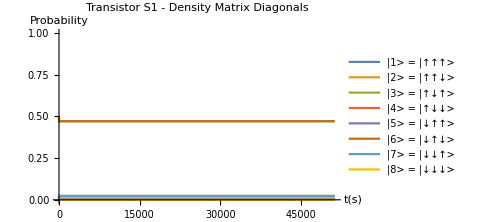
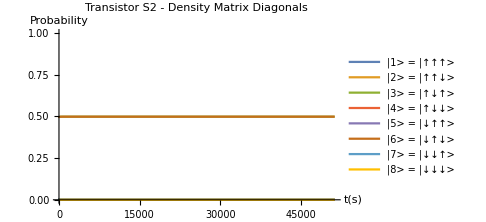

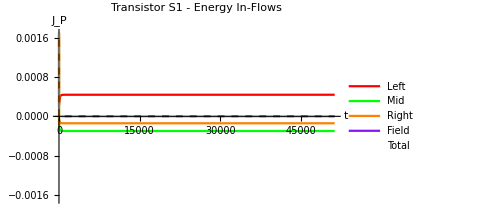
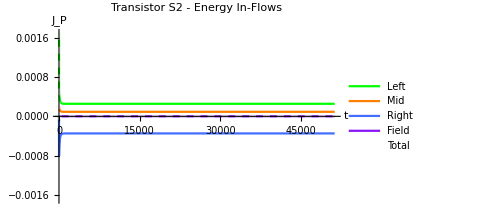

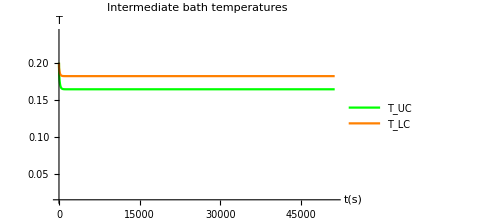

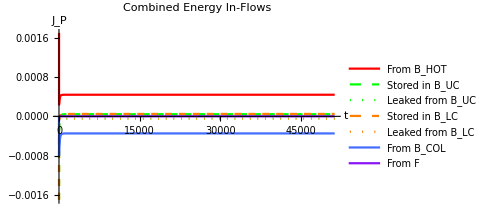

```mathematica
tmax=(41000/Subscript[ωMR, 1])//.Flatten[{unitassum,sysassum}];

motioneqs=Simplify[{Subscript[motioneq, 1],Subscript[motioneq, 2],motioneqintbath}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]];
initconditions={Tuc[0]==Tucinit,Tlc[0]==Tlcinit,Table[Subscript[ρ, S,i,j][0]==0.5 i,j i,3 1+0.5 i,j i,6 1,{S,1,2},{i,1,8},{j,1,8}]}//.Flatten[{sysassum,initassum}];

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, S,i,j],{S,1,2},{i,1,8},{j,1,8}],Tuc,Tlc}],{t,0,tmax}
];

plot1=Flatten[{Table[Subscript[ρ, 1,i,i][t],{i,1,8}]}/.dynamics];
plot2=Flatten[{Table[Subscript[ρ, 2,i,i][t],{i,1,8}]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Transistor S1 - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t(s)"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Transistor S2 - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t(s)"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}]}

plot1=Flatten[{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3],Subscript[EngyFlowInField, 1],Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 1,2]+Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowInField, 1]
}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
plot2=Flatten[{
Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 2,2],Subscript[EngyFlowIn, 2,3],Subscript[EngyFlowInField, 2],Subscript[EngyFlowIn, 2,1]+Subscript[EngyFlowIn, 2,2]+Subscript[EngyFlowIn, 2,3]+Subscript[EngyFlowInField, 2]
}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Transistor S1 - Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv,1.7 10^-3 Econv}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Mid","Right","Field","Total"},
	PlotStyle->{Red,Green,Orange,PurpleC,{White,Dashed}}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Transistor S2 - Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv,1.7 10^-3 Econv}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Mid","Right","Field","Total"},
	PlotStyle->{Green,Orange,BlueC,PurpleC,{White,Dashed}}]}

Flatten[{Tuc[t],Tlc[t]}/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Intermediate bath temperatures"],
	PlotRange-> {0.8Tcol/.sysassum,1.2Thot/.sysassum},
	AxesLabel->{Style["t(s)"],Style["T"]},
	PlotStyle->{Green,Orange},
	PlotLegends->{"T_UC","T_LC"}
]

Flatten[{
Subscript[EngyFlowIn, 1,1],
-(Subscript[EngyFlowIn, 1,2]+Subscript[EngyFlowIn, 2,1]),-Luc(Tuc[t]-Tcol),
-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2]),-Llc(Tlc[t]-Tcol),
Subscript[EngyFlowIn, 2,3],
Subscript[EngyFlowInField, 1]+Subscript[EngyFlowInField, 2]
}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Combined Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv,1.7 10^-3 Econv}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"From B_HOT","Stored in B_UC","Leaked from B_UC","Stored in B_LC","Leaked from B_LC","From B_COL","From F"},
	PlotStyle->{Red,{Green,Dashed},{Green,Dotted},{Orange,Dashed},{Orange,Dotted},BlueC,PurpleC}]
```

#### Initial condition - Both control baths are initially cold

```mathematica
initassum={
Tucinit->0.05 Tconv,Tlcinit->0.05 Tconv
};
```

Numerical solution of the dynamics, with the initial density matrix near a thermal equilibrium system.

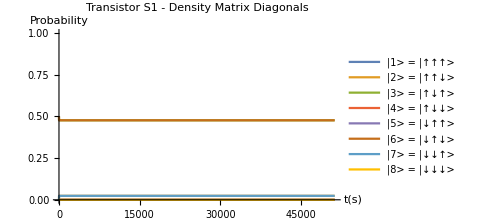
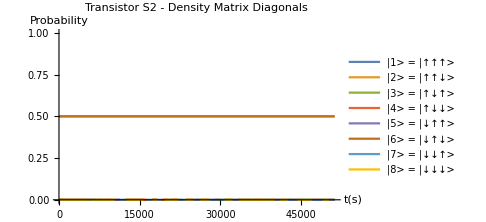

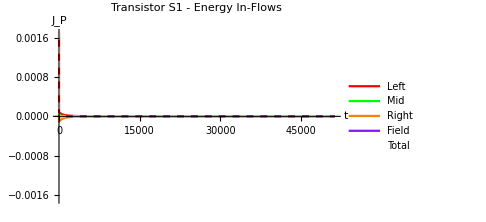
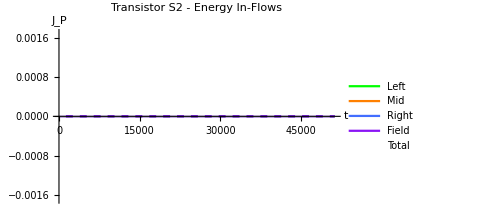

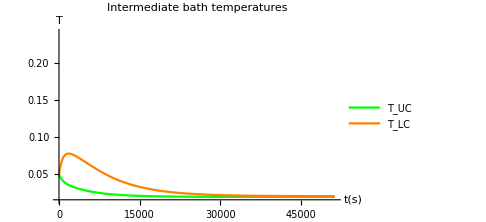

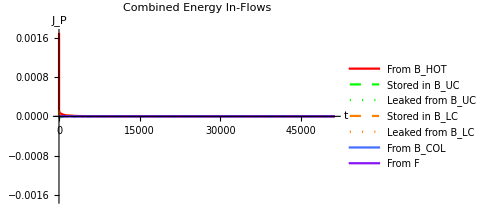

```mathematica
tmax=(41000/Subscript[ωMR, 1])//.Flatten[{unitassum,sysassum}];

motioneqs=Simplify[{Subscript[motioneq, 1],Subscript[motioneq, 2],motioneqintbath}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]];
initconditions={Tuc[0]==Tucinit,Tlc[0]==Tlcinit,Table[Subscript[ρ, S,i,j][0]==0.5 i,j i,3 1+0.5 i,j i,6 1,{S,1,2},{i,1,8},{j,1,8}]}//.Flatten[{sysassum,initassum}];

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, S,i,j],{S,1,2},{i,1,8},{j,1,8}],Tuc,Tlc}],{t,0,tmax}
];

plot1=Flatten[{Table[Subscript[ρ, 1,i,i][t],{i,1,8}]}/.dynamics];
plot2=Flatten[{Table[Subscript[ρ, 2,i,i][t],{i,1,8}]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Transistor S1 - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t(s)"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Transistor S2 - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t(s)"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}]}

plot1=Flatten[{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3],Subscript[EngyFlowInField, 1],Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 1,2]+Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowInField, 1]
}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
plot2=Flatten[{
Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 2,2],Subscript[EngyFlowIn, 2,3],Subscript[EngyFlowInField, 2],Subscript[EngyFlowIn, 2,1]+Subscript[EngyFlowIn, 2,2]+Subscript[EngyFlowIn, 2,3]+Subscript[EngyFlowInField, 2]
}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Transistor S1 - Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv,1.7 10^-3 Econv}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Mid","Right","Field","Total"},
	PlotStyle->{Red,Green,Orange,PurpleC,{White,Dashed}}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Transistor S2 - Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv,1.7 10^-3 Econv}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Mid","Right","Field","Total"},
	PlotStyle->{Green,Orange,BlueC,PurpleC,{White,Dashed}}]}

Flatten[{Tuc[t],Tlc[t]}/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Intermediate bath temperatures"],
	PlotRange-> {0.8Tcol/.sysassum,1.2Thot/.sysassum},
	AxesLabel->{Style["t(s)"],Style["T"]},
	PlotStyle->{Green,Orange},
	PlotLegends->{"T_UC","T_LC"}
]

Flatten[{
Subscript[EngyFlowIn, 1,1],
-(Subscript[EngyFlowIn, 1,2]+Subscript[EngyFlowIn, 2,1]),-Luc(Tuc[t]-Tcol),
-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2]),-Llc(Tlc[t]-Tcol),
Subscript[EngyFlowIn, 2,3],
Subscript[EngyFlowInField, 1]+Subscript[EngyFlowInField, 2]
}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Combined Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv,1.7 10^-3 Econv}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"From B_HOT","Stored in B_UC","Leaked from B_UC","Stored in B_LC","Leaked from B_LC","From B_COL","From F"},
	PlotStyle->{Red,{Green,Dashed},{Green,Dotted},{Orange,Dashed},{Orange,Dotted},BlueC,PurpleC}]
```

## Density matrix, transition rate and energy flow at equilibrium

### Simulation of individual components at steady state

Function for density matrix elements, transition rates and energy flows,

```mathematica
Subscript[varFunc, S_][T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Ωs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,ωassum,NBEassum,unitassum,Subscript[κ, S,1]-> κ1,Subscript[κ, S,2]-> κ2,Subscript[κ, S,3]-> κ3,Subscript[Ω, S]->Ωs,Subscript[T, S,1]-> T1,Subscript[T, S,2]-> T2,Subscript[T, S,3]-> T3,Subscript[ωL, S]->ωLs,Subscript[ωM, S]->ωMs,Subscript[ωR, S]->ωRs,Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs,Subscript[ωRL, S]->ωRLs}];
temp1=N[Subscript[motioneq, S]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, S,i_,j_]'[t]-> 0,Subscript[ρ, S,i_,j_][t]-> Subscript[ρ, S,i,j]},1==∑_(i=1)^8 Subscript[ρ, S,i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, S,i,j],{i,1,8},{j,1,8}]]]]];
Re[{Flatten[
Table[Subscript[ρ, S,i,i],{i,1,8}]/.temp3],
Flatten[{
Subscript[Τs, S,1][5,1],Subscript[Τs, S,1][6,2],Subscript[Τs, S,1][7,3],Subscript[Τs, S,1][8,4],
Subscript[Τs, S,2][3,1],Subscript[Τs, S,2][4,2],Subscript[Τs, S,2][7,5],Subscript[Τs, S,2][8,6],
Subscript[Τs, S,3][2,1],Subscript[Τs, S,3][4,3],Subscript[Τs, S,3][6,5],Subscript[Τs, S,3][8,7],
Subscript[Υs, S][3,1],Subscript[Υs, S][4,2],Subscript[Υs, S][7,5],Subscript[Υs, S][8,6]
}//.Flatten[{Subscript[ρ, S,i_,j_][t]->Subscript[ρ, S,i,j],temp0}]/.temp3],
Flatten[{
Subscript[EngyFlowIn, S,1],Subscript[EngyFlowIn, S,2],Subscript[EngyFlowIn, S,3],Subscript[EngyFlowInField, S]
}//.Flatten[{Subscript[ρ, S,i_,j_][t]->Subscript[ρ, S,i,j],ωassum1,temp0}]/.temp3]}]
]
```

Function for drawing a state flow diagram,

```mathematica
DrawFlowGraph[label_,posx_,posy_,nodes_,rates_,ratecolors_,ratesF_,ratecolorsF_,title_,maxrate_]:=Module[{pos,psize},
psize=Dimensions[label][[1]];
pos[i_]:={posx[[i]],posy[[i]]};
Graphics[Flatten[{
{Thickness[0.0001],Arrowheads[0.03],Black,Arrow[{{1.15Min[posx],1.2Min[posy]},{1.15Min[posx],1.1Max[posy]}}]},Black,{Text[Style["Energy",FontSize->13.6,FontFamily->"Times New Roman"],{1.0Min[posx]-0.03,1.15Max[posy]}],Text[Style[title,FontSize->13.6,FontFamily->"Times New Roman"],{0,1.27Min[posy]}]},

Table[{Opacity[1],Thick,RGBColor[0.55,0.55,0.55],Disk[pos[i],0.01+0.22 √nodes[[i]]]},{i,1,psize}],
Table[
	If[rates[[i,j]]≠0 ,
		If[ ratesF[[i,j]]≠0,
			If[Abs[rates[[i,j]]]>Abs[ratesF[[i,j]]],
				{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			,
				{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			]
		,
			{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
			ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		]
	,
		If[ ratesF[[i,j]]≠0,
			{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
			ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		, Nothing]
	]
,{i,1,psize-1},{j,i+1,psize}],
Table[{Opacity[1],Black,Text[Style[label[[i]],FontSize->12],{posx[[i]]+{0,0.04,0,0.06,0.04,0,0.04,0}[[i]],posy[[i]]+{0.045,0.08,-0.05,-0.06,0.06,-0.05,-0.08,0.045}[[i]]}]},{i,1,psize}]

}], ImageSize->Medium]
]

DrawFunc[S_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,title_,colors_,maxrate_,var_]:=Module[{label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF},temp0=Flatten[{ωassum1,Subscript[ωL, S]->ωLs,Subscript[ωM, S]->ωMs,Subscript[ωR, S]->ωRs,Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs,Subscript[ωRL, S]->ωRLs}];label={"|↑↑↑>","|↑↑↓>","|↑↓↑>","|↑↓↓>","|↓↑↑>","|↓↑↓>","|↓↓↑>","|↓↓↓>"};posx={0.15,-0.4,0.15,0.45,0.6,-0.15,-0.6,-0.15};posy=Table[Subscript[ω, S,i]/ωconv,{i,1,8}]//.temp0;nodes=var[[1]];rates=({{0, -var[[2]][[9]], -var[[2]][[5]], 0, -var[[2]][[1]], 0, 0, 0}, {0, 0, 0, -var[[2]][[6]], 0, -var[[2]][[2]], 0, 0}, {0, 0, 0, -var[[2]][[10]], 0, 0, -var[[2]][[3]], 0}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[4]]}, {0, 0, 0, 0, 0, -var[[2]][[11]], -var[[2]][[7]], 0}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[8]]}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[12]]}, {0, 0, 0, 0, 0, 0, 0, 0}});
ratesF=({{0, 0, -var[[2]][[13]], 0, 0, 0, 0, 0}, {0, 0, 0, -var[[2]][[14]], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -var[[2]][[15]], 0}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[16]]}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});ratecolors=({{0, colors[[3]], colors[[2]], 0, colors[[1]], 0, 0, 0}, {0, 0, 0, colors[[2]], 0, colors[[1]], 0, 0}, {0, 0, 0, colors[[3]], 0, 0, colors[[1]], 0}, {0, 0, 0, 0, 0, 0, 0, colors[[1]]}, {0, 0, 0, 0, 0, colors[[3]], colors[[2]], 0}, {0, 0, 0, 0, 0, 0, 0, colors[[2]]}, {0, 0, 0, 0, 0, 0, 0, colors[[3]]}, {0, 0, 0, 0, 0, 0, 0, 0}});
ratecolorsF=({{0, 0, colors[[4]], 0, 0, 0, 0, 0}, {0, 0, 0, colors[[4]], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, colors[[4]], 0}, {0, 0, 0, 0, 0, 0, 0, colors[[4]]}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
DrawFlowGraph[label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,title,maxrate]
]
```

Simulation for SI units

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
Lconv=(Tconv k^2)/ℏ/.unitassum;
```

Simulation for natural units

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
Lconv=1;
```

#### Steady-state energy flows, transition rates, density matrix diagonals and energy eigenvalues of individual transistors, assuming T_UC and T_LC are artificially fixed

```mathematica
Manipulate[Module[{tempS1,tempS2},
tempS1=Subscript[varFunc, 1][Thot,Tuc,Tlc,κhot,κuc,κlc,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,unitassum];
tempS2=Subscript[varFunc, 2][Tuc,Tlc,Tcol,κuc,κlc,κcol,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum];
{
DrawFunc[1,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,StringForm["Transistor 1"],{Red,Green,Orange,PurpleC},Τmax,tempS1],
DrawFunc[2,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,StringForm["Transistor 2"],{Green,Orange,BlueC,PurpleC},Τmax,tempS2],
BarChart[tempS1[[3]]
,ChartLabels->{"T1 - Left ","T1 - Mid","T1 - Right","T1 - Field"},PlotLabel->"Transistor 1 Energy inflows",AxesLabel->{"","J_P(J)"},ImageSize->Medium,PlotRange->{-Emax1,Emax1},ChartStyle->{Red,Green,Orange,PurpleC}],
BarChart[tempS2[[3]]
,ChartLabels->{"T2 - Left ","T2 - Mid","T2 - Right","T2 - Field"},PlotLabel->"Transistor 2 Energy inflows",AxesLabel->{"","J_P(J)"},ImageSize->Medium,PlotRange->{-Emax2,Emax2},ChartStyle->{Green,Orange,BlueC,PurpleC}],
BarChart[{ -tempS1[[3,2]],-tempS2[[3,1]],-Luc(Tuc-Tcol),-tempS1[[3,2]]-tempS2[[3,1]]-Luc(Tuc-Tcol)}
,ChartLabels->{"T1 - Mid","T2 - Left","Leakage","Total inflow"},PlotLabel->"Energy inflows to B_UC",AxesLabel->{"","J_P(J)"},AxesOrigin->{0,0},ImageSize->Medium,PlotRange->{-Emaxint,Emaxint},ChartStyle->{Yellow,Brown,Gray,White}],
BarChart[{ -tempS1[[3,3]],-tempS2[[3,2]],-Llc(Tlc-Tcol),-tempS1[[3,3]]-tempS2[[3,2]]-Llc(Tlc-Tcol)}
,ChartLabels->{"T1 - Right","T2 - Mid","Leakage","Total inflow"},PlotLabel->"Energy inflows to B_LC",AxesLabel->{"","J_P(J)"},AxesOrigin->{0,0},ImageSize->Medium,PlotRange->{-Emaxint,Emaxint},ChartStyle->{Yellow,Brown,Gray,White}]
}
],
Delimiter,Item["Fixed Bath Temperatures",Alignment->Center],
{{Thot,0.20 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcol,0.02 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Intermediate Bath Temperatures",Alignment->Center],
{{Tuc,0.125 Tconv},0.01 Tconv,0.22 Tconv},
{{Tlc,0.175 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Intermediate Bath Leakage Factors",Alignment->Center],
{{Luc,0Lconv},0.0 Lconv,0.0002 Lconv},
{{Llc,0.0001 Lconv},0.0 Lconv,0.0002 Lconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κhot,1},0.001,2},
{{κcol,1},0.001,2},
{{κuc,1},0.001,2},
{{κlc,1},0.001,2},
Delimiter,Item["Transistor 1 - Parameters",Alignment->Center],
{{ωL1,0.0ωconv},0ωconv,2ωconv},
{{ωM1,0.0ωconv},0ωconv,2ωconv},
{{ωR1,0.0ωconv},0ωconv,2ωconv},
{{ωLM1,0.9ωconv},0ωconv,2ωconv},
{{ωMR1,1.1ωconv},0ωconv,2ωconv},
{{ωRL1,0.0ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor 1 - Optical Field",Alignment->Center],
{{Ω1,0.0ωconv},0ωconv,ωconv},
Delimiter,Item["Transistor 2 - Parameters",Alignment->Center],
{{ωL2,0.0ωconv},0ωconv,2ωconv},
{{ωM2,0.0ωconv},0ωconv,2ωconv},
{{ωR2,0.0ωconv},0ωconv,2ωconv},
{{ωLM2,0.9ωconv},0ωconv,2ωconv},
{{ωMR2,1.1ωconv},0ωconv,2ωconv},
{{ωRL2,0ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor 2 - Optical Field",Alignment->Center],
{{Ω2,0ωconv},0ωconv,ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax1,0.0001Econv},0.00001Econv,0.002Econv},
{{Emax2,0.0001Econv},0.00001Econv,0.002Econv},
{{Emaxint,0.0001Econv},0.00001Econv,0.002Econv},
{{Τmax,0.0008Τconv},0.0001Τconv,0.02Τconv}]
```

### Simulation of combined system at steady state

```mathematica
Module[{Thot,Tcol,Tucinits,Tlcinits,κhot,κuc,κlc,κcol,Luc,Llc,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2},
ωL1=0 ωconv;ωM1=0 ωconv;ωR1=0 ωconv;ωLM1=0.9 ωconv;ωMR1=1.1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0 ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
Tucinits=0.02 Tconv;Tlcinits=0.02 Tconv;
κhot=1;κcol=1;κuc=1;κlc=1;
Luc=0.0001Lconv;Llc=0.0001Lconv;
combinedVarFunc[Thot,Tcol,Tucinits,Tlcinits,κhot,κuc,κlc,κcol,Luc,Llc,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum]
]
```

combinedVarFunc[0.2,0.02,0.02,0.02,1,1,1,1,0.0001,0.0001,0,0,0,0.9,1.1,0,0,0,0,0,0.9,1.1,0,0,{k→1,ℏ→1}]

Conditions for the steady state solutions. The time derivatives have all become zero.

```mathematica
statassum=Flatten[{
Tuc'[t]->0,Tuc[t]->Tuc,
Tlc'[t]->0,Tlc[t]->Tlc,
Table[Subscript[ρ, S,i,j]'[t]->0,{S,1,2},{i,1,8},{j,1,8}],
Table[Subscript[ρ, S,i,j][t]->Subscript[ρ, S,i,j],{S,1,2},{i,1,8},{j,1,8}]
}];
```

Conditions for the density matrices to be valid.

```mathematica
Subscript[denmateq, S_]:=∑_(i=1)^8 Subscript[ρ, S,i,i]==1
```

The equations of motion consists of
	2×56 off diagonal equations, 
	2×7 diagonal equations (one is removed since not all 8 equations are independent of each other), 
	2 density matrix trace equations, 
	2 equations for the upper and lower intermediate baths

```mathematica
stateqns=Expand[Flatten[{
Subscript[motioneqoffdiag, 1],Subscript[motioneqoffdiag, 2],
Subscript[motioneqdiag, 1][[1;;7]],Subscript[motioneqdiag, 2][[1;;7]],
Subscript[denmateq, 1],Subscript[denmateq, 2],
motioneqintbath}]];
```

Generate starting point for the equation solver

```mathematica
startpoints:=Module[{temp},
temp=Flatten[Table[{Subscript[ρ, S,i,j],0.5 i,j i,3 1+0.5 i,j i,6 1},{S,1,2},{i,1,8},{j,1,8}],2];
AppendTo[temp,{Tuc,Tucinit}];
AppendTo[temp,{Tlc,Tlcinit}]
]
```

```mathematica
combinedVarFunc[Thots_,Tcols_,Tucinits_,Tlcinits_,κhots_,κucs_,κlcs_,κcols_,Lucs_,Llcs_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,Ω1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,unitassum_]:=
Module[{temp0,temp1,temp2},
temp0=Flatten[{statassum,unitassum,Jassum,NBEassum,ωassum,ωassum1,Tassum,
Thot->Thots,Tcol->Tcols,
κhot->κhots,κuc->κucs,κlc->κlcs,κcol->κcols,
Luc->Lucs,Llc->Llcs,
Subscript[ωL, 1]->ωL1,Subscript[ωM, 1]->ωM1,Subscript[ωR, 1]->ωR1,Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,Subscript[ωRL, 1]->ωRL1,Subscript[Ω, 1]->Ω1,
Subscript[ωL, 2]->ωL2,Subscript[ωM, 2]->ωM2,Subscript[ωR, 2]->ωR2,Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,Subscript[ωRL, 2]->ωRL2,Subscript[Ω, 2]->Ω2}];

temp1=stateqns//.temp0;
temp2=Quiet[FindRoot[temp1,startpoints/.{Tucinit->Tucinits,Tlcinit->Tlcinits},WorkingPrecision->20]];
Re[{{Tuc,Tlc}//.temp2,Table[{
	Table[Subscript[ρ, S,i,i],{i,1,8}]/.temp2,
	{
		Subscript[Τs, S,1][5,1],Subscript[Τs, S,1][6,2],Subscript[Τs, S,1][7,3],Subscript[Τs, S,1][8,4],
		Subscript[Τs, S,2][3,1],Subscript[Τs, S,2][4,2],Subscript[Τs, S,2][7,5],Subscript[Τs, S,2][8,6],
		Subscript[Τs, S,3][2,1],Subscript[Τs, S,3][4,3],Subscript[Τs, S,3][6,5],Subscript[Τs, S,3][8,7],
		Subscript[Υs, S][3,1],Subscript[Υs, S][4,2],Subscript[Υs, S][7,5],Subscript[Υs, S][8,6]
	}//.Flatten[{temp0,temp2}],
	{
		Subscript[EngyFlowIn, S,1],Subscript[EngyFlowIn, S,2],Subscript[EngyFlowIn, S,3],Subscript[EngyFlowInField, S]
	}//.Flatten[{temp0,temp2}]
},{S,1,2}]
}]
]
```

```mathematica
Manipulate[Module[{temp},
temp=combinedVarFunc[Thot,Tcol,Tucinit,Tlcinit,κhot,κuc,κlc,κcol,Luc,Llc,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum];
{
DrawFunc[1,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,StringForm["Transistor 1"],{Red,Green,Orange,PurpleC},Τmax,temp[[2,1]]],
DrawFunc[2,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,StringForm["Transistor 2"],{Red,Orange,BlueC,PurpleC},Τmax,temp[[2,2]]],
BarChart[temp[[2,1,3]]
,ChartLabels->{"T1 - Left ","T1 - Mid","T1 - Right","T1 - Field"},PlotLabel->"Transistor 1 Energy inflows",AxesLabel->{"","J_P(J)"},ImageSize->Medium,PlotRange->{-Emax1,Emax1},ChartStyle->{Red,Green,Orange,PurpleC}],
BarChart[temp[[2,2,3]]
,ChartLabels->{"T2 - Left ","T2 - Mid","T2 - Right","T2 - Field"},PlotLabel->"Transistor 2 Energy inflows",AxesLabel->{"","J_P(J)"},ImageSize->Medium,PlotRange->{-Emax2,Emax2},ChartStyle->{Green,Orange,BlueC,PurpleC}],
BarChart[{ -temp[[2,1,3,2]],-temp[[3,1]],-Luc(Tuc-Tcol),-tempS1[[3,2]]-tempS2[[3,1]]-Luc(Tuc-Tcol)}
,ChartLabels->{"T1 - Mid","T2 - Left","Leakage","Total inflow"},PlotLabel->"Energy inflows to B_UC",AxesLabel->{"","J_P(J)"},AxesOrigin->{0,0},ImageSize->Medium,PlotRange->{-Emaxint,Emaxint},ChartStyle->{Yellow,Brown,Gray,White}],
BarChart[{ -tempS1[[3,3]],-tempS2[[3,2]],-Llc(Tlc-Tcol),-tempS1[[3,3]]-tempS2[[3,2]]-Llc(Tlc-Tcol)}
,ChartLabels->{"T1 - Right","T2 - Mid","Leakage","Total inflow"},PlotLabel->"Energy inflows to B_LC",AxesLabel->{"","J_P(J)"},AxesOrigin->{0,0},ImageSize->Medium,PlotRange->{-Emaxint,Emaxint},ChartStyle->{Yellow,Brown,Gray,White}]
StringForm["{Tuc,Tlc}=``",NumberForm[temp[[1]],4]]
}
],
Delimiter,Item["Fixed Bath Temperatures",Alignment->Center],
{{Thot,0.20 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcol,0.02 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Initial Control Temperatures",Alignment->Center],
{{Tucinit,0.20 Tconv},0.02 Tconv,0.20 Tconv},
{{Tlcinit,0.20 Tconv},0.02 Tconv,0.20 Tconv},
Delimiter,Item["Intermediate Bath Leakage Factors",Alignment->Center],
{{Luc,0.0001Lconv},0.0 Lconv,0.0002 Lconv},
{{Llc,0.0001 Lconv},0.0 Lconv,0.0002 Lconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κhot,1},0.001,2},
{{κcol,1},0.001,2},
{{κuc,1},0.001,2},
{{κlc,1},0.001,2},
Delimiter,Item["Transistor 1 - Parameters",Alignment->Center],
{{ωL1,0.0ωconv},0ωconv,2ωconv},
{{ωM1,0.0ωconv},0ωconv,2ωconv},
{{ωR1,0.0ωconv},0ωconv,2ωconv},
{{ωLM1,0.6ωconv},0ωconv,2ωconv},
{{ωMR1,0.8ωconv},0ωconv,2ωconv},
{{ωRL1,0.0ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor 1 - Optical Field",Alignment->Center],
{{Ω1,0.0ωconv},0ωconv,ωconv},
Delimiter,Item["Transistor 2 - Parameters",Alignment->Center],
{{ωL2,0.0ωconv},0ωconv,2ωconv},
{{ωM2,0.0ωconv},0ωconv,2ωconv},
{{ωR2,0.0ωconv},0ωconv,2ωconv},
{{ωLM2,0.9ωconv},0ωconv,2ωconv},
{{ωMR2,1.1ωconv},0ωconv,2ωconv},
{{ωRL2,0ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor 2 - Optical Field",Alignment->Center],
{{Ω2,0ωconv},0ωconv,ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax1,0.0011Econv},0.00001Econv,0.002Econv},
{{Emax2,0.0011Econv},0.00001Econv,0.002Econv},
{{Τmax,0.0038Τconv},0.0001Τconv,0.02Τconv},
ContinuousAction->False]
```

## Energy flows when intermediate bath temperatures are fixed